# Regression and Other Stories

## Chapter 1.

```mathematica
hibbs=SemanticImport[FileNameJoin[{$UserDocumentsDirectory, "hibbs.csv"}], Automatic,"Dataset", HeaderLines->1, Delimiters->","]
```

The variable growth are  the values of x ranging from 0 to 4%

```mathematica
growth := hibbs[All, "growth"]//Normal
vote := hibbs[All, "inc.party.vote"]//Normal
data = Transpose[{growth, vote}];
```

Incumbent.party.vote as a function of growth

```mathematica
model=GeneralizedLinearModelFit[data,x,x, ExponentialFamily->"Gaussian"]
```

FittedModel[46.2476+3.06053 x]

The values 46.2476 and 3.0 are the coefficients in the fitted line y = 46.2476 + 3.0 x

```mathematica
Normal[model]
```

46.2476+3.06053 x

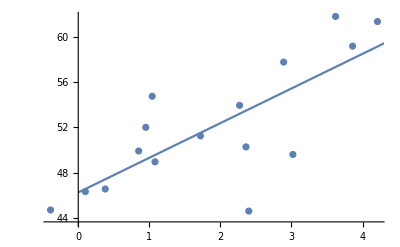

```mathematica
Show[ListPlot[data],Plot[model[x],{x,0,5}]]
```

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | z-Statistic | P-Value
1 | 46.2476 | 1.62193 | 28.5139 | 7.8699×10^-179
x | 3.06053 | 0.696274 | 4.39558 | 0.0000110477

Sigma is the Residual Standard Deviation

```mathematica
StandardDeviation[model["FitResiduals"]]
```

3.63568

## Exercises

## 1.8

### 1.1

```mathematica
helicopters=SemanticImport[FileNameJoin[{$UserDocumentsDirectory, "helicopters.txt"}], Automatic,"Dataset", HeaderLines->1, Delimiters->" "]
```

### 1.2

```mathematica
y[x_] := 30 + 20x
```

```mathematica
growth := hibbs[All, "growth"]//Normal
vote := hibbs[All, "inc.party.vote"]//Normal
data = Transpose[{growth, vote}];
```

```mathematica
model = GeneralizedLinearModelFit[data,x,x, ExponentialFamily->"Gaussian"]
```

FittedModel[46.2476+3.06053 x]

```mathematica
Normal[model]
```

46.2476+3.06053 x

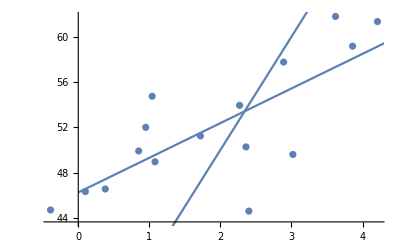

```mathematica
Show[ListPlot[data], Plot[model[x], {x,0,5}], Plot[30+10x, {x,0,5}]]
```